# DM DM -> h2 h2

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMEWSB.mod

> 54 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 112 vertices

classes model {SDdiracDMEWSB} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1: 2 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

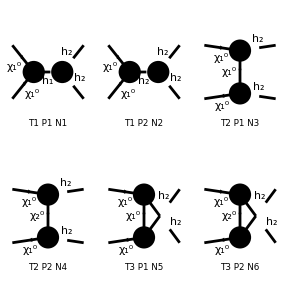

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | [T1 P2 N2] | [T2 P1 N3]
[T2 P2 N4] | [T3 P1 N5] | [T3 P2 N6])]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{S[1,{2}],S[1,{2}]}, InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz"(*,ExcludeParticles->{S[1,{1}],F[6,{2}] }*) ];
Paint[d22,ColumnsXRows->{3,2}]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 6 Particles amplitudes

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True];
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-8.frm

running FORM...

ok

#### Rotation matrices

```mathematica
Den[x_,y_]:=1/(x-y)
expr1=Simplify[ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)/.{MassFxv[1]->mx1,MassFxv[2]->mx2,Masshh[1]->mh1,Masshh[2]->mh2}/.{ZH[1,1]->Z11,ZH[1,2]->Z12,ZH[2,1]->-Z12,ZH[2,2]->Z11}/.{XV[1,1]->V11,XV[1,2]->V12,XV[2,1]->-V12,XV[2,2]->V11}/.{XU[1,1]->U11,XU[1,2]->U12,XU[2,1]->-U12,XU[2,2]->U11}]/.(Z11^2+Z12^2)->1
```

1/4 ((mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (-S V12 YRC+mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12))+3 Lam vvSM Z12^2 (-S V11 YRD+mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))) Mat[<v2|1|u1>]-(mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2) Mat[<v2|5|u1>])/((mx2^2-T) (mx2^2-U))+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(2 U12^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx1^2+T)+(2 U12^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx1^2-U)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx2^2-T)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx2^2+U)+(4 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx1^2-T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(4 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx1^2+U)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(2 U12^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx1^2+T)+(2 U12^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx1^2-U)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+T)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-U)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+T)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-U)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U))

#### Kind of Dirac Chains in the AMPLITUDE

```mathematica
InputForm[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->0}]
```

0

```mathematica
expr2 = Simplify[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->F1,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->F5,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->F13,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->F53}]
```

1/4 ((F53 U12^2 V11^2 YRC^2 Z11^2)/(mx2^2-T)+(F13 U12^2 V11^2 YRC^2 Z11^2)/(-mx2^2+T)+(F13 U12^2 V11^2 YRC^2 Z11^2)/(mx2^2-U)+(F53 U12^2 V11^2 YRC^2 Z11^2)/(-mx2^2+U)+(F13 U11^2 V12^2 YRC^2 Z11^2)/(-mx2^2+T)+(F53 U11^2 V12^2 YRC^2 Z11^2)/(-mx2^2+T)+(F13 U11^2 V12^2 YRC^2 Z11^2)/(mx2^2-U)+(F53 U11^2 V12^2 YRC^2 Z11^2)/(mx2^2-U)+(2 F13 U12^2 V12^2 YRC^2 Z11^2)/(-mx1^2+T)+(2 F13 U12^2 V12^2 YRC^2 Z11^2)/(mx1^2-U)+(2 F13 U11^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F53 U11^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F13 U11^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(2 F53 U11^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(4 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx1^2-T)+(2 F53 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+T)+(2 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-U)+(4 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx1^2+U)+(2 F53 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(F13 U11^2 V11^2 YRD^2 Z12^2)/(-mx2^2+T)+(F53 U11^2 V11^2 YRD^2 Z12^2)/(-mx2^2+T)+(F13 U11^2 V11^2 YRD^2 Z12^2)/(mx2^2-U)+(F53 U11^2 V11^2 YRD^2 Z12^2)/(mx2^2-U)+(2 F13 U12^2 V11^2 YRD^2 Z12^2)/(-mx1^2+T)+(2 F13 U12^2 V11^2 YRD^2 Z12^2)/(mx1^2-U)+(F53 U12^2 V12^2 YRD^2 Z12^2)/(mx2^2-T)+(F13 U12^2 V12^2 YRD^2 Z12^2)/(-mx2^2+T)+(F13 U12^2 V12^2 YRD^2 Z12^2)/(mx2^2-U)+(F53 U12^2 V12^2 YRD^2 Z12^2)/(-mx2^2+U)-(F5 mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/((mx2^2-T) (mx2^2-U))+F1 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (-S V12 YRC+mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12))+3 Lam vvSM Z12^2 (-S V11 YRD+mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))))

#### Factors in the AMPLITUDE

```mathematica
M1=Simplify[D[expr2,F1]]
```

1/4 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (-S V12 YRC+mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12))+3 Lam vvSM Z12^2 (-S V11 YRD+mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))

```mathematica
M2=Simplify[D[expr2,F5]]
```

-(mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))

```mathematica
M3=Simplify[D[expr2,F13]]
```

1/4 (-((T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (2/(mx1^2-T)+1/(-mx2^2+T)+1/(mx2^2-U)+2/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V12^2 (-(2 (T-U) YRC^2 Z11^2)/((mx1^2-T) (mx1^2-U))+(1/(-mx2^2+T)+1/(mx2^2-U)) YRD^2 Z12^2)+V11^2 ((1/(-mx2^2+T)+1/(mx2^2-U)) YRC^2 Z11^2+(2 (-T+U) YRD^2 Z12^2)/((mx1^2-T) (mx1^2-U)))))

```mathematica
M4=Simplify[D[expr2,F53]]
```

((T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))

#### Factorization of the Amplitude

```mathematica
expr3 =(M1*F1+M2*F5+M3*F13+M4*F53);
```

```mathematica
Simplify[expr2 -expr3]
```

0

## Momenta in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==Sqrt[p1^2+mx1^2]&&E2==Sqrt[p2^2+mh2^2]&& E2==E1},{E1,E2,p2}][[1]]
```

{E1→√(mx1^2+p1^2),E2→√(mx1^2+p1^2),p2→-√(-mh2^2+mx1^2+p1^2)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E2,p2*ct,p2*st,0}/.st->Sqrt[1-ct^2];
k4={E2,-p2*ct,-p2*st,0}/.st->Sqrt[1-ct^2];
```

#### Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		         T->(k1 - k3).guv.(k1 - k3),   
                            U ->(k1 - k4).guv.(k1 - k4)}/.kinematic]
```

{S→4 (mx1^2+p1^2),T→mh2^2-mx1^2-2 p1 (p1+ct √(-mh2^2+mx1^2+p1^2)),U→mh2^2-mx1^2-2 p1 (p1-ct √(-mh2^2+mx1^2+p1^2))}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinors (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+mx1));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+mx1));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mx1));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+mx1));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,mx1,k2[[1]]]
```

{√(E1+mx1),0,0,-p1/(√(E1+mx1))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,mx1,k2[[1]]]
```

{0,-p1/(√(E1+mx1)),√(E1+mx1),0}

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.uspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,mx1,k2[[1]]]]).gamma0.uspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.uspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,mx1,k4[[1]]]]).gamma0.uspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

2 mx1

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.vspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,mx1,k3[[1]]]]).gamma0.vspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,mx1,k4[[1]]]]).gamma0.vspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

-2 mx1

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,mx1,k3[[1]]]
AA2=(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,mx1,k1[[1]]]
Simplify[Conjugate[AA1]-AA2]
```

-(ⅈ (ct p2+ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(√(E2+mx1))+ⅈ √(E2+mx1) (1/(√(E1+mx1)))^* p1^*

-(ⅈ p1 (√(E2+mx1))^*)/(√(E1+mx1))+ⅈ √(E1+mx1) (1/(√(E2+mx1)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*)

0

```mathematica
BB1=Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,mx1,k3[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]
BB2=Simplify[(Conjugate[vspinor[1,σp4,mx1,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,mx1,k1[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]
Simplify[Simplify[(Conjugate[BB1]-BB2),Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]]
```

ⅈ (p1+(ct+ⅈ √(1-ct^2)) p2)

-ⅈ (p1+ct p2-ⅈ p2 (√(1-ct^2))^*)

0

## Amplitude square

Manipulation of the amplitude

#### Dirac Chains in the amplitude (F1,F5,F13,F53)

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]
```

Mat[<v2|1|u1>]

Mat[<v2|5|u1>]

Mat[<v2|1,k[3]|u1>]

Mat[<v2|5,k[3]|u1>]

#### FULL Amplitude

```mathematica
AMP[s1_,s2_]:=expr3/.{
F1->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[1]]]],
F5->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],uspinor[s1,σp1,mx1,k1[[1]]]],
F13->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,(k3[[1]]*gamma0-k3[[2]]*gamma1-k3[[3]]*gamma2-k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]],
F53->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5,(k3[[1]]*gamma0-k3[[2]]*gamma1-k3[[3]]*gamma2-k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]]
}
```

```mathematica
AMP[1,-1]
```

1/4 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (-S V12 YRC+mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12))+3 Lam vvSM Z12^2 (-S V11 YRD+mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))) (-(p1 (√(E1+mx1))^*)/(√(E1+mx1))-√(E1+mx1) (1/(√(E1+mx1)))^* p1^*)+1/4 (-((T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (2/(mx1^2-T)+1/(-mx2^2+T)+1/(mx2^2-U)+2/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V12^2 (-(2 (T-U) YRC^2 Z11^2)/((mx1^2-T) (mx1^2-U))+(1/(-mx2^2+T)+1/(mx2^2-U)) YRD^2 Z12^2)+V11^2 ((1/(-mx2^2+T)+1/(mx2^2-U)) YRC^2 Z11^2+(2 (-T+U) YRD^2 Z12^2)/((mx1^2-T) (mx1^2-U))))) (√(E1+mx1) ((-ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*-E2 (1/(√(E1+mx1)))^* p1^*)+(p1 (E2 (√(E1+mx1))^*-(-ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*))/(√(E1+mx1)))

Sum over spinors and gamma matrices.. trick! Warning: I do the gamma matrices explicitly because i need to avoid the index in the gamma_uv.

#### FULL Amplitude squared

```mathematica
AMP2=(1/4)*(Sum[AMP[s1,s2]*Conjugate[AMP[s1,s2]],{s1,{-1,1}},{s2,{-1,1}}]/.{√(1-ct^2)->st})/.{Conjugate[mx1]->mx1,Conjugate[mx2]->mx2,Conjugate[mh1]->mh1,Conjugate[mh2]->mh2,Conjugate[√(E1+mx1)]->√(E1+mx1),Conjugate[1/(√(E1+mx1))]->1/(√(E1+mx1)),Conjugate[E1]->E1,Conjugate[E2]->E2,Conjugate[p1]->p1,Conjugate[p2]->p2,Conjugate[st]->st,Conjugate[ct]->ct,Conjugate[Lam]->Lam,Conjugate[Z11]->Z11,Conjugate[Z12]->Z12,Conjugate[Z21]->Z21,Conjugate[Z22]->Z22,Conjugate[vvSM]->vvSM,Conjugate[LSP]->LSP,Conjugate[LSPH]->LSPH}/.{st->Sqrt[1-ct^2],Z22->Z11,Z21->-Z12};
```

## Check of the amplitude square

## Differential cross section approximation

```mathematica
expr4=AMP2/.kinematic/.MV;
```

```mathematica
expr5=expr4/.p1->mx1*v;
```

```mathematica
expr6=Normal[Series[expr5,{v,0,2}]];
```

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
dcs=(1/(64 π^2 S)*((S-(mh2+mh2)^2)/(S-(mx1+mx1)^2))^(1/2)*expr6)/.MV/.p1->mx1*v;
```

Multiply by the velocity and expand

```mathematica
vdcs=v*dcs;
```

```mathematica
Simplify[Normal[Series[vdcs,{v,0,1}]]]
```

0

```mathematica
expr7= Normal[Series[vdcs,{v,0,2}]]
```

1/(1024 mx1^2 π^2)√(1-mh2^2/mx1^2) v^2 ((1/4 √(mx1+√(mx1^2)) (ct √(-mh2^2+mx1^2) √(mx1+√(mx1^2))+ⅈ √(1-ct^2) √(-mh2^2+mx1^2) √(mx1+√(mx1^2))) ((4 ct mx1 √(-mh2^2+mx1^2) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((-mh2^2+mx1^2+mx2^2)^2)+U12^2 ((4 ct mx1 √(-mh2^2+mx1^2) V11^2 YRC^2 Z11^2)/((-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) V12^2 YRC^2 Z11^2)/((-mh2^2+2 mx1^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) (-mh2^4+2 mx1^4+4 mh2^2 mx2^2-4 mx1^2 mx2^2-2 mx2^4) V11 V12 YRC YRD Z11 Z12)/((-mh2^2+2 mx1^2)^2 (-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) V11^2 YRD^2 Z12^2)/((-mh2^2+2 mx1^2)^2)+(4 ct mx1 √(-mh2^2+mx1^2) V12^2 YRD^2 Z12^2)/((-mh2^2+mx1^2+mx2^2)^2)))+1/2 mx1 (-mx1 (-(2 U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/(mh2^2-mx1^2-mx2^2)+U12^2 (2 (8/(mh2^2-2 mx1^2)+2/(-mh2^2+mx1^2+mx2^2)) V11 V12 YRC YRD Z11 Z12+V11^2 ((2 YRC^2 Z11^2)/(-mh2^2+mx1^2+mx2^2)-(8 YRD^2 Z12^2)/(mh2^2-2 mx1^2))+V12^2 (-(8 YRC^2 Z11^2)/(mh2^2-2 mx1^2)+(2 YRD^2 Z12^2)/(-mh2^2+mx1^2+mx2^2))))-2 U12 (-(2 mx2 U11 (-V11 V12 YRC^2 Z11^2+V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 YRD^2 Z12^2))/(-mh2^2+mx1^2+mx2^2)-1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 (-12 LSP mx1^2 V12 vS YRC Z11^2+3 LSP mh1^2 V12 vS YRC Z11^4-3 LSP mh1^2 V11 vS YRD Z11^3 Z12+3 LSP mh2^2 V11 vS YRD Z11^3 Z12-12 Lam mx1^2 V11 vvSM YRD Z12^2+3 LSP mh2^2 V12 vS YRC Z11^2 Z12^2+3 Lam mh2^2 V11 vvSM YRD Z11^2 Z12^2-3 Lam mh1^2 V12 vvSM YRC Z11 Z12^3+3 Lam mh2^2 V12 vvSM YRC Z11 Z12^3+3 Lam mh1^2 V11 vvSM YRD Z12^4+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-4 mx1^2 (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))) (1/4 √(mx1+√(mx1^2)) (ct √(-mh2^2+mx1^2) √(mx1+√(mx1^2))-ⅈ √(1-ct^2) √(-mh2^2+mx1^2) √(mx1+√(mx1^2))) ((4 ct mx1 √(-mh2^2+mx1^2) (U11^*)^2 (-YRD Z12 V11^*+YRC Z11 V12^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)+(U12^*)^2 ((4 ct mx1 √(-mh2^2+mx1^2) YRC^2 Z11^2 (V11^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) YRD^2 Z12^2 (V11^*)^2)/((-mh2^2+2 mx1^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) (-mh2^4+2 mx1^4+4 mh2^2 mx2^2-4 mx1^2 mx2^2-2 mx2^4) YRC YRD Z11 Z12 V11^* V12^*)/((-mh2^2+2 mx1^2)^2 (-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) YRC^2 Z11^2 (V12^*)^2)/((-mh2^2+2 mx1^2)^2)+(4 ct mx1 √(-mh2^2+mx1^2) YRD^2 Z12^2 (V12^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)))+1/2 mx1 (-mx1 (-(2 (U11^*)^2 (YRD Z12 V11^*-YRC Z11 V12^*)^2)/(mh2^2-mx1^2-mx2^2)+(U12^*)^2 (((2 YRC^2 Z11^2)/(-mh2^2+mx1^2+mx2^2)-(8 YRD^2 Z12^2)/(mh2^2-2 mx1^2)) (V11^*)^2+2 (8/(mh2^2-2 mx1^2)+2/(-mh2^2+mx1^2+mx2^2)) YRC YRD Z11 Z12 V11^* V12^*+(-(8 YRC^2 Z11^2)/(mh2^2-2 mx1^2)+(2 YRD^2 Z12^2)/(-mh2^2+mx1^2+mx2^2)) (V12^*)^2))-2 U12^* ((2 mx2 U11^* (-YRC YRD Z11 Z12 (V11^*)^2+YRC^2 Z11^2 V11^* V12^*-YRD^2 Z12^2 V11^* V12^*+YRC YRD Z11 Z12 (V12^*)^2))/(-mh2^2+mx1^2+mx2^2)-1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 (-3 LSP mh1^2 vS YRD Z11^3 Z12 V11^*+3 LSP mh2^2 vS YRD Z11^3 Z12 V11^*-12 Lam mx1^2 vvSM YRD Z12^2 V11^*+3 Lam mh2^2 vvSM YRD Z11^2 Z12^2 V11^*+3 Lam mh1^2 vvSM YRD Z12^4 V11^*-12 LSP mx1^2 vS YRC Z11^2 V12^*+3 LSP mh1^2 vS YRC Z11^4 V12^*+3 LSP mh2^2 vS YRC Z11^2 Z12^2 V12^*-3 Lam mh1^2 vvSM YRC Z11 Z12^3 V12^*+3 Lam mh2^2 vvSM YRC Z11 Z12^3 V12^*+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (-YRD Z12 V11^*+YRC Z11 V12^*)+mh2^2 (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)) (YRD Z11 V11^*+YRC Z12 V12^*)-4 mx1^2 (YRD Z11 (vvSM Z11-2 vS Z12) V11^*+YRC Z12 (-2 vvSM Z11+vS Z12) V12^*))))))+(1/4 √(mx1+√(mx1^2)) (ct √(-mh2^2+mx1^2) √(mx1+√(mx1^2))-ⅈ √(1-ct^2) √(-mh2^2+mx1^2) √(mx1+√(mx1^2))) ((4 ct mx1 √(-mh2^2+mx1^2) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((-mh2^2+mx1^2+mx2^2)^2)+U12^2 ((4 ct mx1 √(-mh2^2+mx1^2) V11^2 YRC^2 Z11^2)/((-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) V12^2 YRC^2 Z11^2)/((-mh2^2+2 mx1^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) (-mh2^4+2 mx1^4+4 mh2^2 mx2^2-4 mx1^2 mx2^2-2 mx2^4) V11 V12 YRC YRD Z11 Z12)/((-mh2^2+2 mx1^2)^2 (-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) V11^2 YRD^2 Z12^2)/((-mh2^2+2 mx1^2)^2)+(4 ct mx1 √(-mh2^2+mx1^2) V12^2 YRD^2 Z12^2)/((-mh2^2+mx1^2+mx2^2)^2)))+1/2 mx1 (-mx1 (-(2 U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/(mh2^2-mx1^2-mx2^2)+U12^2 (2 (8/(mh2^2-2 mx1^2)+2/(-mh2^2+mx1^2+mx2^2)) V11 V12 YRC YRD Z11 Z12+V11^2 ((2 YRC^2 Z11^2)/(-mh2^2+mx1^2+mx2^2)-(8 YRD^2 Z12^2)/(mh2^2-2 mx1^2))+V12^2 (-(8 YRC^2 Z11^2)/(mh2^2-2 mx1^2)+(2 YRD^2 Z12^2)/(-mh2^2+mx1^2+mx2^2))))-2 U12 (-(2 mx2 U11 (-V11 V12 YRC^2 Z11^2+V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 YRD^2 Z12^2))/(-mh2^2+mx1^2+mx2^2)-1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 (-12 LSP mx1^2 V12 vS YRC Z11^2+3 LSP mh1^2 V12 vS YRC Z11^4-3 LSP mh1^2 V11 vS YRD Z11^3 Z12+3 LSP mh2^2 V11 vS YRD Z11^3 Z12-12 Lam mx1^2 V11 vvSM YRD Z12^2+3 LSP mh2^2 V12 vS YRC Z11^2 Z12^2+3 Lam mh2^2 V11 vvSM YRD Z11^2 Z12^2-3 Lam mh1^2 V12 vvSM YRC Z11 Z12^3+3 Lam mh2^2 V12 vvSM YRC Z11 Z12^3+3 Lam mh1^2 V11 vvSM YRD Z12^4+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-4 mx1^2 (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))) (1/4 √(mx1+√(mx1^2)) (ct √(-mh2^2+mx1^2) √(mx1+√(mx1^2))+ⅈ √(1-ct^2) √(-mh2^2+mx1^2) √(mx1+√(mx1^2))) ((4 ct mx1 √(-mh2^2+mx1^2) (U11^*)^2 (-YRD Z12 V11^*+YRC Z11 V12^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)+(U12^*)^2 ((4 ct mx1 √(-mh2^2+mx1^2) YRC^2 Z11^2 (V11^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) YRD^2 Z12^2 (V11^*)^2)/((-mh2^2+2 mx1^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) (-mh2^4+2 mx1^4+4 mh2^2 mx2^2-4 mx1^2 mx2^2-2 mx2^4) YRC YRD Z11 Z12 V11^* V12^*)/((-mh2^2+2 mx1^2)^2 (-mh2^2+mx1^2+mx2^2)^2)+(8 ct mx1 √(-mh2^2+mx1^2) YRC^2 Z11^2 (V12^*)^2)/((-mh2^2+2 mx1^2)^2)+(4 ct mx1 √(-mh2^2+mx1^2) YRD^2 Z12^2 (V12^*)^2)/((-mh2^2+mx1^2+mx2^2)^2)))+1/2 mx1 (-mx1 (-(2 (U11^*)^2 (YRD Z12 V11^*-YRC Z11 V12^*)^2)/(mh2^2-mx1^2-mx2^2)+(U12^*)^2 (((2 YRC^2 Z11^2)/(-mh2^2+mx1^2+mx2^2)-(8 YRD^2 Z12^2)/(mh2^2-2 mx1^2)) (V11^*)^2+2 (8/(mh2^2-2 mx1^2)+2/(-mh2^2+mx1^2+mx2^2)) YRC YRD Z11 Z12 V11^* V12^*+(-(8 YRC^2 Z11^2)/(mh2^2-2 mx1^2)+(2 YRD^2 Z12^2)/(-mh2^2+mx1^2+mx2^2)) (V12^*)^2))-2 U12^* ((2 mx2 U11^* (-YRC YRD Z11 Z12 (V11^*)^2+YRC^2 Z11^2 V11^* V12^*-YRD^2 Z12^2 V11^* V12^*+YRC YRD Z11 Z12 (V12^*)^2))/(-mh2^2+mx1^2+mx2^2)-1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 (-3 LSP mh1^2 vS YRD Z11^3 Z12 V11^*+3 LSP mh2^2 vS YRD Z11^3 Z12 V11^*-12 Lam mx1^2 vvSM YRD Z12^2 V11^*+3 Lam mh2^2 vvSM YRD Z11^2 Z12^2 V11^*+3 Lam mh1^2 vvSM YRD Z12^4 V11^*-12 LSP mx1^2 vS YRC Z11^2 V12^*+3 LSP mh1^2 vS YRC Z11^4 V12^*+3 LSP mh2^2 vS YRC Z11^2 Z12^2 V12^*-3 Lam mh1^2 vvSM YRC Z11 Z12^3 V12^*+3 Lam mh2^2 vvSM YRC Z11 Z12^3 V12^*+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (-YRD Z12 V11^*+YRC Z11 V12^*)+mh2^2 (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)) (YRD Z11 V11^*+YRC Z12 V12^*)-4 mx1^2 (YRD Z11 (vvSM Z11-2 vS Z12) V11^*+YRC Z12 (-2 vvSM Z11+vS Z12) V12^*)))))))

No mixing in the fermion sector

```mathematica
expr8=Simplify[expr7/.{LSP->0, YRD->0,U11->0,U12->1,V11->0,V12->1},{mx1>0}]
```

1/(512 π^2)√(1-mh2^2/mx1^2) v^2 YRC^2 ((4 mx1 YRC Z11^2)/(mh2^2-2 mx1^2)+(4 ct (ct-ⅈ √(1-ct^2)) mx1 (-mh2^2+mx1^2) YRC Z11^2)/((mh2^2-2 mx1^2)^2)+1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))) ((4 mx1 YRC Z11^2)/(mh2^2-2 mx1^2)+(4 ct (ct+ⅈ √(1-ct^2)) mx1 (-mh2^2+mx1^2) YRC Z11^2)/((mh2^2-2 mx1^2)^2)+1/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))√2 Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3))))

#### The cross - section is p - wave in general with the contribution of the S, t and U channel. The limit U and T channel is

```mathematica
(*expr8=Simplify[expr7/.{Lam->0,LSP->0,LSPH->0, YRD->0,U11->0,U12->1,V11->0,V12->1}]*)
```

(√(1-mh2^2/mx1^2) mx1^2 ((1-ct^2+ⅈ ct √(1-ct^2)) mh2^2+(-2+ct^2-ⅈ ct √(1-ct^2)) mx1^2) ((1-ct^2-ⅈ ct √(1-ct^2)) mh2^2+(-2+ct^2+ⅈ ct √(1-ct^2)) mx1^2) v^2 YRC^4 Z11^4)/(32 (mh2^2-2 mx1^2)^4 π^2)

## Cross section

```mathematica
σv=(-∫_1^-1 (expr8)*(2π)ⅆct)
```

-(√(1-mh2^2/mx1^2) v^2 YRC^2 (-(32 mh1^4 mh2^8 mx1^2 YRC^2 Z11^4)/((-mh2^2+2 mx1^2)^4 (-mh1^2+4 mx1^2)^2 (-mh2^2+4 mx1^2)^2)+(384 4 Z11^4)/1+506+(16 (71+4 √2 5 Z11^2 Z12^4))/(3 (-mh2^2+1)^4 (-mh1^2+4 1) (-mh2^2+4 mx1^2))))/(256 π)
 |  |  |  |

```mathematica
Muy larga... pero satisface el limite U-T channel
```

```mathematica
Simplify[σv/.{Lam->0,LSPH->0}]
```

(√(1-mh2^2/mx1^2) mx1^2 (2 mh2^4-8 mh2^2 mx1^2+9 mx1^4) v^2 YRC^4 Z11^4)/(24 (mh2^2-2 mx1^2)^4 π)

```mathematica
AA=Normal[Series[Simplify[σv],{v,0,4}]]
```

(√(1-mh2^2/mx1^2) mx1^2 (2 mh2^4-8 mh2^2 mx1^2+9 mx1^4) v^2 YRC^4 Z11^4)/(24 (mh2^2-2 mx1^2)^4 π)

```mathematica
σvr=Simplify[(AA/2)/.{v->vr/2}]
```

(√(1-mh2^2/mx1^2) mx1^2 (2 mh2^4-8 mh2^2 mx1^2+9 mx1^4) vr^2 YRC^4 Z11^4)/(192 (mh2^2-2 mx1^2)^4 π)

```mathematica
AAA=FullSimplify[σvr/.{mh2->μ*mx1},mx1>0]
```

(vr^2 YRC^4 Z11^4 √(1-μ^2) (9-8 μ^2+2 μ^4))/(192 mx1^2 π (-2+μ^2)^4)

```mathematica
Grid[{{"σvr"},{AAA/.YRC->hc}},Frame->All]
```

σvr
(hc^4 vr^2 Z11^4 √(1-μ^2) (9-8 μ^2+2 μ^4))/(192 mx1^2 π (-2+μ^2)^4)

```mathematica
FullSimplify[σvr/.{(2 mh2^4-8 mh2^2 mx1^2+9 mx1^4)->(9 mx1^4)}/.{mh2->μ*mx1}]
```

(3 vr^2 YRC^4 Z11^4 √(1-μ^2))/(64 mx1^2 π (-2+μ^2)^4)